# The costs of a bacterial envelope

We distinguish between three kinds of costs:
1. Opportunity cost of oxidizing the precursor molecule
2. Opportunity cost of missed synthesis of ATP from NAD(P)H
3. Direct cost of ATP hydrolysis to power chemical transformation

Precursors ⟶ compounds synthesized in glycolysis, TCA, PPP pathways (including glycerol and glycerol 3-phosphate)
All other compounds have costs partially expressed in terms of precursor molecules from which they are produced. Precursors do not have direct and synthesis costs.

## Precursor metabolite costs

#### Electron transport chain behavior

```mathematica
(* Conversion scheme from: Mahmoudabadi et al. 2018 *)
nadphCost[x_]=x*2;
fadh2Cost[x_]=x*1;
(* Nelson and Cox 2005; pp. 607 *)
costCoA[n_]=n(1+nadphCost[3]+fadh2Cost[1]) (* cost of running one round of TCA *);
```

#### Glycolysis compounds

```mathematica
glucoseCost[x_]=x*(2+nadphCost[4]+costCoA[2]) (* 2 ATP and 2 NADH in glycolisis, 2 NADH in conversion to 2*AcCoA, and 2 AcCoA in TCA *);
f6pCost[x_]=x*(glucoseCost[1]+1) (* same as glucose, but with an additional ATP spent to modify it; cost are the same for glucose 6-P *);
pyruvateCost[x_]=x*(nadphCost[1]+costCoA[1]) (* cost of pyruvate = cost(AcCoA) + nadph, since the latter is needed to convert pyruvate to AcCoA *);
pepCost[x_]=x*(pyruvateCost[1]+1) (* pyruvate + 1 ATP lost in converting PEP to Pyr *);
dhapCosts[x_]=x*(2+nadphCost[1]+nadphCost[1]+costCoA[1]);
g3pCosts[x_]=dhapCosts[x] (* 2 ATP + 1 NADH in payoff phase of glycolysis + 1 NADH during conversion of pyruvate to AcCoA *);
threepgCost[x_]=x*(1+nadphCost[1]+costCoA[1]) (* 1 ATP in payoff phase, 1 NADH in conversion to AcCoA, and then oxidation of AcCoA *);
```

#### TCA compounds

Oxaloacetate biosynthesis: https://biocyc.org/GCF_000953615/NEW-IMAGE?type=REACTION&object=PEPCARBOXYKIN-RXN

```mathematica
oaaCost[x_]=x*(pepCost[1]-1)  (* phosphorylating oxaloacetate yields PEP *);
```

#### Glycolysis branch-off pathway

GroP biosynthesis: https://biocyc.org/ECOLI/NEW-IMAGE?type=REACTION&object=RXN0-5410

```mathematica
(* Total costs *)
groPCosts[x_]=x*(g3pCosts[1]+nadphCost[1]) (* glycerol-3-P is made by reducing g3p *);
glycerolCost[x_]=x*(groPCosts[1]-1);
```

#### Pentose phosphate pathway

ADP-heptose biosynthesis:
https://biocyc.org/ECOLI/NEW-IMAGE?type=PATHWAY&object=PWY0-1241

```mathematica
r5pCost[x_]=x*(glucoseCost[1]+1-nadphCost[2]) (* Nelson and Cox 2005, pp. 550; G6P is converted into ribulose 5-P with two additional 2 NADPH being produced *);
s7pCost[x_]=x*(r5pCost[2]-g3pCosts[1]) (* Nelson and Cox 2005, pp. 552; converting r5p and x5p to glyceraldehyde-3-p and sedoheptulose-7-p; thus the cost of s7p is cost of r5p and x5p minus the cost of glyceraldehyde3p. Note that x5p and r5p have the same cost since they are interconverted by epimerase with no additional energy required *);
heptoseCost[x_]=x*(s7pCost[1]+2) (* conversion to ADP-heptose requires expenditure of 2 ATPs *);
```

```mathematica
heptoseCostPrec[x_]=x*(s7pCost[1]);
heptoseCostSyn[x_]=x*(0);
heptoseCostDir[x_]=x*(2);
```

#### Intermolecular conversion costs

Note that this result differs compared to Mahmoudabadi et al. 2018, because they do not include 1 NADH in Glu-to-αkg conversion.

```mathematica
costAlphatoGlu[x_]=nadphCost[x]+x(* Nelson and Cox 2005, pp. 838; converting α-ketoglutarate to glutamate requires 1 ATP and 1 NADPH; so every time amino a glutamate is converted to αkg has to be accompanied by expenditure of 1 NADH and 1 ATP regenerate the lost glutamate *);
glnTogluCost[x_]=x (* glutamate is converted to glutamine with expenditure of 1 ATP *);
```

```mathematica
costAlphatoGluSyn[x_]=nadphCost[x];
costAlphatoGluDir[x_]=x;
```

## Building block costs

Format of each cell:
1^st line → total cost
2^nd line → precursor costs
3^rd line → synthesis costs
4^th line → direct costs

#### Amino acid biosynthesis

```mathematica
aspCost[x_]=x*(oaaCost[1]+costAlphatoGlu[1]);
aspCostPrec[x_]=x*(oaaCost[1]);
aspCostSyn[x_]=x*(costAlphatoGluSyn[1]);
aspCostDir[x_]=x*(costAlphatoGluDir[1]);
```

```mathematica
ileCost[x_]=x(aspCost[1]+pyruvateCost[1]+nadphCost[3]+2+costAlphatoGlu[1]);
ileCostPrec[x_]=x*(aspCostPrec[1]+pyruvateCost[1]);
ileCostSyn[x_]=x*(aspCostSyn[1]+nadphCost[3]+costAlphatoGluSyn[1]);
ileCostDir[x_]=x*(2+costAlphatoGluDir[1]+aspCostDir[1]) (* 2 ATPs used directly and 1 required to regenerate αkg to Glu *);
```

```mathematica
valCost[x_]=x(pyruvateCost[2]+nadphCost[1]+costAlphatoGlu[1]);
valCostPrec[x_]=x*(pyruvateCost[2]);
valCostSyn[x_]=x*(nadphCost[1]+costAlphatoGluSyn[1]);
valCostDir[x_]=x*(costAlphatoGluDir[1]);
```

```mathematica
serCost[x_]=x*(threepgCost[1]+costAlphatoGlu[1]-nadphCost[1]) (* subtracting nadph cost because nadh is generated in the first step *);
serCostPrec[x_]=x*threepgCost[1];
serCostSyn[x_]=x*(costAlphatoGluSyn[1]-nadphCost[1]);
serCostDir[x_]=x*costAlphatoGluDir[1];
```

```mathematica
lysineCost[x_]=x*(aspCost[1]+pyruvateCost[1]+costAlphatoGlu[1]+1+nadphCost[2]);
lysineCostPrec[x_]=x*(aspCostPrec[1]+pyruvateCost[1]);lysineCostSyn[x_]=x*(aspCostSyn[1]+costAlphatoGluSyn[1]+nadphCost[2]);lysineCostDir[x_]=x*(1+costAlphatoGluDir[1]+aspCostDir[1]);
```

#### Acyl tail biosynthesis

#### Primers and extenders

```mathematica
malonylCoaCost[x_]=costCoA[x]+x (* Nelson and Cox 2005, pp. 788; 1 ATP is expended to attach COO^- to acetyl-CoA *);
malonylCoaCostPrec[x_]=costCoA[x]; 
malonylCoaCostSyn[x_]=x*0;
malonylCoaCostDir[x_]=x;
```

Biosynthesis of α-ketovaline (primer for iso-branched fatty acids):
https://bsubcyc.org/BSUB/NEW-IMAGE?type=REACTION&object=BRANCHED-CHAINAMINOTRANSFERVAL-RXN

```mathematica
isoPrimerCost[x_]=x(valCost[1]-nadphCost[1]-costAlphatoGlu[1]) (* Nelson and Cox 2005, pp. 683; α-keto acid biosynthesis; subtracting the costs of 1 NADH and 1 conversion because (1) branched chain α-ketoacid dehydrogenase generates 1 NADH, and (2) amino group is transfered to α-ketoglutarate to make ketoacid of valine. *);
isoPrimerCostPrec[x_]=x(valCostPrec[1]) ;
isoPrimerCostSyn[x_]=x(valCostSyn[1]-nadphCost[1]-costAlphatoGluSyn[1]);
isoPrimerCostDir[x_]=x(valCostDir[1]-costAlphatoGluDir[1]);
```

Biosynthesis of 2-keto-isoleucine (primer for anteiso-branched fatty acids):
https://bsubcyc.org/BSUB/NEW-IMAGE?type=REACTION&object=BRANCHED-CHAINAMINOTRANSFERILEU-RXN

```mathematica
anteisoPrimerCost[x_]=x(ileCost[1]-nadphCost[1]+costAlphatoGlu[1]);
anteisoPrimerCostPrec[x_]=x(ileCostPrec[1]);
anteisoPrimerCostSyn[x_]=x(ileCostSyn[1]-nadphCost[1]+costAlphatoGluSyn[1]);
anteisoPrimerCostDir[x_]=x(ileCostDir[1]+costAlphatoGluDir[1]);
```

#### Acyl chain synthesis

```mathematica
normalCost[x_,n_]=x(costCoA[1]+malonylCoaCost[(n-2)/2]+nadphCost[(n-2)]) (* Nelson and Cox 2005, pp. 793 *);
normalCostPrec[x_,n_]=x(costCoA[1]+malonylCoaCostPrec[(n-2)/2]);
normalCostSyn[x_,n_]=x(malonylCoaCostSyn[(n-2)/2]+nadphCost[(n-2)]) ;
normalCostDir[x_,n_]=x(malonylCoaCostDir[(n-2)/2]) ;
```

```mathematica
anteisoCost[x_,n_]=x(anteisoPrimerCost[1]+malonylCoaCost[(n-3)/2]+nadphCost[(n-3)]) (* the logic of synthesis is the same, save for the fact that primer has 3C atoms *);
anteisoCostPrec[x_,n_]=x(anteisoPrimerCostPrec[1]+malonylCoaCostPrec[(n-3)/2]);
anteisoCostSyn[x_,n_]=x(anteisoPrimerCostSyn[1]+malonylCoaCostSyn[(n-3)/2]+nadphCost[(n-3)]);
anteisoCostDir[x_,n_]=x(anteisoPrimerCostDir[1]+malonylCoaCostDir[(n-3)/2]);
```

```mathematica
isoCost[x_,n_]=x(isoPrimerCost[1]+malonylCoaCost[(n-3)/2]+nadphCost[(n-3)]);
isoCostPrec[x_,n_]=x(isoPrimerCostPrec[1]+malonylCoaCostPrec[(n-3)/2]);isoCostSyn[x_,n_]=x(isoPrimerCostSyn[1]+malonylCoaCostSyn[(n-3)/2]+nadphCost[(n-3)]);isoCostDir[x_,n_]=x(isoPrimerCostDir[1]+malonylCoaCostDir[(n-3)/2]);
```

#### Lipid head group biosynthesis

References for head groups:
PG synthesis (https://biocyc.org/GCF_000953615/NEW-IMAGE?type=PATHWAY&object=PWY4FS-8)
PE synthesis (https://biocyc.org/GCF_000953615/NEW-IMAGE?type=PATHWAY&object=PWY-5669)
CL synthesis (https://biocyc.org/ECOLI/NEW-IMAGE?type=PATHWAY&object=PWY-5668&detail-level=3)
Lys-PG synthesis (https://biocyc.org/GCF_000953615/NEW-IMAGE?type=REACTION&object=LYSYLTRANSFERASE-RXN)

```mathematica
pgCost[x_]=x*(dhapCosts[1]+groPCosts[1]+nadphCost[1]+2) (* 2 ATPs come from the fact that CTP enters the system but CMP exits *);
pgCostPrec[x_]=x*(dhapCosts[1]+groPCosts[1]);
pgCostSyn[x_]=x*(nadphCost[1]);
pgCostDir[x_]=x*(2);
```

```mathematica
dagCost[x_]=pgCost[x]-groPCosts[1] (* dag cost is the same as pg cost minus the GroP introduced in second-to-last step; see above link on PG synthesis *);
dagCostPrec[x_]=pgCostPrec[x]-groPCosts[1];
dagCostSyn[x_]=pgCostSyn[x];
dagCostDir[x_]=pgCostDir[x];
```

```mathematica
peCost[x_]=x*(dagCost[1]+serCost[1]);
peCostPrec[x_]=x*(dagCost[1]+serCost[1]);
peCostSyn[x_]=x*(dagCostSyn[1]+serCostSyn[1]);
peCostDir[x_]=x*(dagCostDir[1]+serCostDir[1]);
```

```mathematica
cardiolipinCost[x_]=x*(dagCost[2]+groPCosts[2]-glycerolCost[1]);
cardiolipinCostPrec[x_]=x*(dagCostPrec[2]+groPCosts[2]-glycerolCost[1]);
cardiolipinCostSyn[x_]=x*(dagCostSyn[2]);
cardiolipinCostDir[x_]=x*(dagCostDir[2]);
```

```mathematica
lysPGCost[x_]=x*(pgCost[1]+lysineCost[1])+x (* plus 1 in the end comes from having to spend 1 ATP to charge tRNA with Lys, which is the substrate used to produce Lys-PG *);
lysPGCostPrec[x_]=x*(pgCost[1]+lysineCost[1]);
lysPGCostSyn[x_]=x*(pgCostSyn[1]+lysineCostSyn[1]);
lysPGCostDir[x_]=x*(pgCostDir[1]+lysineCostDir[1]);
```

#### Disaccharides and short peptides

References for production of disaccharides:
GlcNAc synthesis: https://www.qmul.ac.uk/sbcs/iubmb/enzyme/reaction/polysacc/UDPGlcN.html
Mur2Ac synthesis: Nelson and Cox 2005, pp. 778

Note that these are the costs of nt-activated sugars, but we are not accounting for costs of used UTP because we don’t know whether UDP or UMP exists the reaction when sugars are used. This is accounted separately in processes of:
1. Endotoxin production
2. PGN unit synthesis

```mathematica
(* UDP-GlcNAc *)
```

```mathematica
glcNAcCost[x_]=x*(f6pCost[1]+glnTogluCost[1]+costCoA[1]);
glcNAcCostPrec[x_]=x*(f6pCost[1]+costCoA[1]);
glcNAcCostSyn[x_]=x*(0);
glcNAcCostDir[x_]=x*(1);
```

```mathematica
(* UDP-Mur2Ac *)
```

```mathematica
mur2AcCost[x_]=x*(glcNAcCost[1]+pepCost[1]+nadphCost[1]);
mur2AcCostPrec[x_]=x*(glcNAcCostPrec[1]+pepCost[1]);
mur2AcCostSyn[x_]=x*(nadphCost[1]);
mur2AcCostDir[x_]=x*(glcNAcCostDir[1]);
```

```mathematica
averageAACost=27 (* 27 ATP for synthesis of average amino acid *);
```

```mathematica
peptideStemCost[x_,n_]=x*(averageAACost*n);
peptideStemCostPrec[x_,n_]=x*((averageAACost-2)*n);
peptideStemCostSyn[x_,n_]=x*(0);
peptideStemCostDir[x_,n_]=x*(2*n);
```

```mathematica
kdoCost[x_]=x*(r5pCost[2]+pepCost[2]+2*2) (* Lodowska et al. 2013 -- 2 CTPs are converted to 2 CMPs, hence 2*2 ATPs are spent in total *);
kdoCostPrec[x_]=x*(r5pCost[2]+pepCost[2]);
kdoCostSyn[x_]=x*(0);
kdoCostDir[x_]=x*(2*2);
```

#### Visualizing the metabolite costs

```mathematica
(* Glycolysis pathway *)
glycolysisList=Sort[{glucoseCost[1],f6pCost[1],pyruvateCost[1],pepCost[1],dhapCosts[1],g3pCosts[1],threepgCost[1],groPCosts[1],glycerolCost[1]},Greater];
glycolysisListDir=glycolysisListSyn={0,0,0,0,0,0,0,0,0};
```

```mathematica
barPlotGlycolysisPrecCost=glycolysisList
barPlotGlycolysisSynCost=Map[{barPlotGlycolysisPrecCost[[#]],glycolysisListSyn[[#]]}&,Table[i,{i,1,Length[glycolysisList]}]]
barPlotGlycolysisDirCost=Map[{barPlotGlycolysisPrecCost[[#]]+glycolysisListSyn[[#]],glycolysisListDir[[#]]}&,Table[i,{i,1,Length[glycolysisList]}]]
```

{27,26,16,15,14,14,11,11,10}

{{27,0},{26,0},{16,0},{15,0},{14,0},{14,0},{11,0},{11,0},{10,0}}

{{27,0},{26,0},{16,0},{15,0},{14,0},{14,0},{11,0},{11,0},{10,0}}

```mathematica
(* TCA pathway *)
tcaList=Sort[{costCoA[1],oaaCost[1]},Greater];
tcaListDir=tcaListSyn={0,0};
```

```mathematica
barPlotTcaPrecCost=tcaList
barPlotTcaSynCost=Map[{barPlotTcaPrecCost[[#]],tcaListSyn[[#]]}&,Table[i,{i,1,Length[tcaList]}]]
barPlotTcaDirCost=Map[{barPlotTcaPrecCost[[#]]+tcaListSyn[[#]],tcaListDir[[#]]}&,Table[i,{i,1,Length[tcaList]}]]
```

{10,8}

{{10,0},{8,0}}

{{10,0},{8,0}}

```mathematica
(* Pentose phosphate pathway *)
pentoseList=Sort[{r5pCost[1],s7pCost[1],heptoseCost[1]},Greater];
pentoseListDir={heptoseCostDir[1],0,0};
pentoseListSyn={heptoseCostSyn[1],0,0};
```

```mathematica
barPlotPPPrecCost=pentoseList-(pentoseListSyn+pentoseListDir)
barPlotPPSynCost=Map[{barPlotPPPrecCost[[#]],pentoseListSyn[[#]]}&,Table[i,{i,1,Length[pentoseList]}]]
barPlotPPDirCost=Map[{barPlotPPPrecCost[[#]]+pentoseListSyn[[#]],pentoseListDir[[#]]}&,Table[i,{i,1,Length[pentoseList]}]]
```

{32,32,23}

{{32,0},{32,0},{23,0}}

{{32,2},{32,0},{23,0}}

```mathematica
(* Amino acid biosynthesis pathway *)
aaList=Sort[{aspCost[1],ileCost[1],valCost[1],serCost[1],lysineCost[1]},Greater];
aaListDir={ileCostDir[1],lysineCostDir[1],valCostDir[1],aspCostDir[1],serCostDir[1]};
aaListSyn={ileCostSyn[1],lysineCostSyn[1],valCostSyn[1],aspCostSyn[1],serCostSyn[1]};
```

```mathematica
barPlotAAPrecCost=aaList-(aaListSyn+aaListDir)
barPlotAASynCost=Map[{barPlotAAPrecCost[[#]],aaListSyn[[#]]}&,Table[i,{i,1,Length[aaList]}]]
barPlotAADirCost=Map[{barPlotAAPrecCost[[#]]+aaListSyn[[#]],aaListDir[[#]]}&,Table[i,{i,1,Length[aaList]}]]
```

{20,20,20,10,11}

{{20,10},{20,8},{20,4},{10,2},{11,0}}

{{30,4},{28,3},{24,1},{12,1},{11,1}}

```mathematica
(* FAS primers synthesis *)
primersExtendersList=Sort[{malonylCoaCost[1],isoPrimerCost[1],anteisoPrimerCost[1]},Greater];
primersExtendersListDir={anteisoPrimerCostDir[1],isoPrimerCostDir[1],malonylCoaCostDir[1]};
primersExtendersListSyn={anteisoPrimerCostSyn[1],isoPrimerCostSyn[1],malonylCoaCostSyn[1]};
```

```mathematica
barPlotPrimPrecCost=primersExtendersList-(primersExtendersListSyn+primersExtendersListDir)
barPlotPrimSynCost=Map[{barPlotPrimPrecCost[[#]],primersExtendersListSyn[[#]]}&,Table[i,{i,1,Length[primersExtendersList]}]]
barPlotPrimDirCost=Map[{barPlotPrimPrecCost[[#]]+primersExtendersListSyn[[#]],primersExtendersListDir[[#]]}&,Table[i,{i,1,Length[primersExtendersList]}]]
```

{20,20,8}

{{20,10},{20,0},{8,0}}

{{30,5},{20,0},{8,1}}

```mathematica
(* Lipid head groups *)
headList=Sort[{pgCost[1],dagCost[1],peCost[1],lysPGCost[1],cardiolipinCost[1]},Greater];
headListDir={cardiolipinCostDir[1],lysPGCostDir[1],peCostDir[1],pgCostDir[1],dagCostDir[1]};
headListSyn={cardiolipinCostSyn[1],lysPGCostSyn[1],peCostSyn[1],pgCostSyn[1],dagCostSyn[1]};
```

```mathematica
barPlotHPrecCost=headList-(headListSyn+headListDir)
barPlotHSynCost=Map[{barPlotHPrecCost[[#]],headListSyn[[#]]}&,Table[i,{i,1,Length[headList]}]]
barPlotHDirCost=Map[{barPlotHPrecCost[[#]]+headListSyn[[#]],headListDir[[#]]}&,Table[i,{i,1,Length[headList]}]]
```

{61,51,29,26,14}

{{61,4},{51,10},{29,2},{26,2},{14,2}}

{{65,4},{61,5},{31,3},{28,2},{16,2}}

```mathematica
(* Lipid tail chains *)
acylList={anteisoCost[1,17],N[normalCost[1,19]],normalCost[1,18]+nadphCost[1],anteisoCost[1,15],normalCost[1,18],N[isoCost[1,17]],N[isoCost[1,16]],normalCost[1,16]+nadphCost[1],N[isoCost[1,15]],N[isoCost[1,14]],normalCost[1,14]+nadphCost[1],normalCost[1,14],normalCost[1,14]-nadphCost[1]};
acylListDir={anteisoCostDir[1,17],N[normalCostDir[1,19]],normalCostDir[1,18],anteisoCostDir[1,15],normalCostDir[1,18],N[isoCostDir[1,17]],N[isoCostDir[1,16]],normalCostDir[1,16],N[isoCostDir[1,15]],N[isoCostDir[1,14]],normalCostDir[1,14],normalCostDir[1,14],normalCostDir[1,14]};
acylListSyn={anteisoCostSyn[1,17],N[normalCostSyn[1,19]],normalCostSyn[1,18]+nadphCost[1],anteisoCostSyn[1,15],normalCostSyn[1,18],N[isoCostSyn[1,17]],N[isoCostSyn[1,16]],normalCostSyn[1,16]+nadphCost[1],N[isoCostSyn[1,15]],N[isoCostSyn[1,14]],normalCostSyn[1,14]+nadphCost[1],normalCostSyn[1,14],normalCostSyn[1,14]-nadphCost[1]};
barPlotAcyl=Map[{acylList[[#]]-(acylListSyn[[#]]+acylListDir[[#]]),acylListSyn[[#]],acylListDir[[#]]}&,Table[i,{i,1,Length[acylList]}]];
```

```mathematica
barPlotTPrecCost=acylList-(acylListSyn+acylListDir)
barPlotTSynCost=Map[{barPlotTPrecCost[[#]],acylListSyn[[#]]}&,Table[i,{i,1,Length[acylList]}]]
barPlotTDirCost=Map[{barPlotTPrecCost[[#]]+acylListSyn[[#]],acylListDir[[#]]}&,Table[i,{i,1,Length[acylList]}]]
```

{76,76.,72,68,72,76.,72.,64,68.,64.,56,56,56}

{{76,38},{76.,34.},{72,34},{68,34},{72,32},{76.,28.},{72.,26.},{64,30},{68.,24.},{64.,22.},{56,26},{56,24},{56,22}}

{{114,12},{110.,8.5},{106,8},{102,11},{104,8},{104.,7.},{98.,6.5},{94,7},{92.,6.},{86.,5.5},{82,6},{80,6},{78,6}}

```mathematica
(* Conversion costs *)
conversionCosts=Sort[{glnTogluCost[1],costAlphatoGlu[1],nadphCost[1],fadh2Cost[1]},Greater];
conversionCostsDir=Sort[{glnTogluCost[1],costAlphatoGlu[1],nadphCost[1],fadh2Cost[1]},Greater];
```

```mathematica
(* Sugar derivative costs *)
largerBlocksList={kdoCost[1],mur2AcCost[1],glcNAcCost[1]};
largerBlocksListSyn={kdoCostSyn[1],mur2AcCostSyn[1],glcNAcCostSyn[1]};
largerBlocksListDir={kdoCostDir[1],mur2AcCostDir[1],glcNAcCostDir[1]};
```

```mathematica
barPlotLargePrecCost=largerBlocksList-(largerBlocksListSyn+largerBlocksListDir)
barPlotLargeSynCost=Map[{barPlotLargePrecCost[[#]],largerBlocksListSyn[[#]]}&,Table[i,{i,1,Length[largerBlocksList]}]]
barPlotLargeDirCost=Map[{barPlotLargePrecCost[[#]]+largerBlocksListSyn[[#]],largerBlocksListDir[[#]]}&,Table[i,{i,1,Length[largerBlocksList]}]]
```

{68,46,35}

{{68,0},{46,2},{35,0}}

{{68,4},{48,1},{35,1}}

```mathematica
b1=BarChart[Join[
barPlotGlycolysisPrecCost,{0},
barPlotTcaPrecCost,{0},
barPlotPPPrecCost,{0},
barPlotAAPrecCost,{0},
barPlotLargePrecCost,{0},
barPlotPrimPrecCost,{0},
barPlotHPrecCost,{0},
barPlotTPrecCost],BarSpacing->Medium,ChartStyle->{Directive[EdgeForm[],Darker[Green]]},ImageSize->Full,
Frame->True,
PlotRange->{-5,130},
ChartLabels->
Placed[{
"f6p","glc","grop","gro","dhap","g3p","pep","3pg","pyr","",
"oaa","acCoA","",
"hep","s7p","r5p","",
"ile","lys","val","asp","ser","",
"kdo","mur2Ac","glcNAc","",
"2mbutCoA","isobutCoA","malCoA","",
"cl","lyspg","pe","pg","dag","",
"a17:0","n19:0","n18:1","a15:0","n18:0","i17:0","i16:0","n16:1","i15:0","i14:0","n14:1","n14:0","nhyd14:0"
},
Axis,Rotate[#,Pi/4]&]/.ImageScaled[{1/2,1}]->ImageScaled[{0.9,1}],
FrameLabel->{None,"Cost (ATP molecules)"}
];
```

```mathematica
b2=BarChart[Join[
barPlotGlycolysisSynCost,{{0,0}},
barPlotTcaSynCost,{{0,0}},
barPlotPPSynCost,{{0,0}},
barPlotAASynCost,{{0,0}},
barPlotLargeSynCost,{{0,0}},
barPlotPrimSynCost,{{0,0}},
barPlotHSynCost,{{0,0}},
barPlotTSynCost],ChartLayout->"Stacked",ChartStyle->{Directive[FaceForm[],EdgeForm[]],Darker[Yellow]},BarSpacing->Medium,ImageSize->Full
,PlotRange->{-5,130}];
```

```mathematica
b3=BarChart[Join[
barPlotGlycolysisDirCost,{{0,0}},
barPlotTcaDirCost,{{0,0}},
barPlotPPDirCost,{{0,0}},
barPlotAADirCost,{{0,0}},
barPlotLargeDirCost,{{0,0}},
barPlotPrimDirCost,{{0,0}},
barPlotHDirCost,{{0,0}},
barPlotTDirCost],ChartLayout->"Stacked",ChartStyle->{Directive[FaceForm[],EdgeForm[]],Darker[Blue]},BarSpacing->Medium,ImageSize->Full
,PlotRange->{-5,130}];
```

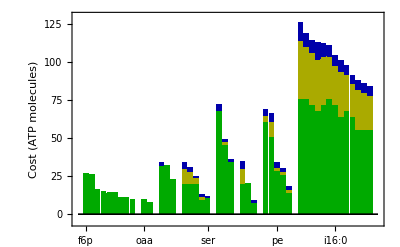

```mathematica
Show[b1,b2,b3]/.Line[{a_,Offset[b_,c_]}]:>Sequence[]
```

## Gram-negative cell wall (data for E. coli)

#### Membrane fatty acid composition

```mathematica
(* Fatty acid composition of E. coli lipids from Pramanik and Keasling 1997 *)
c1400Frac=0.0268 (* myristic *);
c1401Frac=0.07 (* myristoleic -- unsaturated *);
c1600Frac=0.3823 (* palmitic *);
c1601Frac=0.1074 (* palmitoleic -- unsaturated *);
c17ΔFrac=0.1611 (* heptadecanoic *);
c1800Frac=0.09 (* cis-Vaccenic -- unsaturated *);
c1801Frac=0.1791 (* oleic -- unsaturated *);
c19ΔFrac=0.0573 (* nonadecanoic *);
```

#### Making of the endotoxin with KDO linker

```mathematica
(* Anderson and Raetz 1987 *)
lipidACost[x_]=x*(
normalCost[1,12]+ (* lauric acid *)
normalCost[1,14]+ (* myristic acid *)
4*(normalCost[1,14]-nadphCost[1])+ (* β-hydroxymyristic acid -- stop before hydration in the last round *)
2*glcNAcCost[1]+ (* 2 GlcNAc *)
2+1 +(* nt-activation of 2 GlcNAc molecules with 2 UTP; one exists as UDP the other as UMP *)
kdoCost[2] (* 2 CMP-Kdo molecules; counting 2 released CMPs *)
);
```

```mathematica
lipidACostPrec[x_]=x*(
normalCostPrec[1,12]+
normalCostPrec[1,14]+
4*(normalCostPrec[1,14])+ 
2*glcNAcCostPrec[1]+
kdoCostPrec[2] 
);
lipidACostSyn[x_]=x*(
normalCostSyn[1,12]+
normalCostSyn[1,14]+
4*(normalCostSyn[1,14])+ 
2*glcNAcCostSyn[1]+
kdoCostSyn[2] 
-4*nadphCost[1]);
lipidACostDir[x_]=x*(
normalCostDir[1,12]+
normalCostDir[1,14]+
4*(normalCostDir[1,14])+ 
2*glcNAcCostDir[1]+
kdoCostDir[2]+
2+1);
```

```mathematica
lipidACost[1]
lipidACostPrec[1]+lipidACostSyn[1]+lipidACostDir[1]
```

714

714

#### Attaching the polysaccharide core

References:
Inner core ⟶ inner core -- Cote and Taylor 2017
Outer core ⟶ outer core taken for E. coli K12 -- Whitfield et al. 2003.

```mathematica
innerCoreCost[x_]=x*(heptoseCost[3]+1) (* Cote and Taylor 2017 -- phosphorylating C4 of one KDO molecule requires a +1 ATP *);
innerCoreCostPrec[x_]=x*(heptoseCostPrec[3]);
innerCoreCostSyn[x_]=x*(heptoseCostSyn[3]);
innerCoreCostDir[x_]=x*(heptoseCostDir[3]+1);
```

```mathematica
innerCoreCost[1]
innerCoreCostPrec[1]+innerCoreCostSyn[1]+innerCoreCostDir[1]
```

103

103

UDP-Glucose synthesis ⟶ https://ecocyc.org/ECOLI/NEW-IMAGE?type=REACTION&object=GLUC1PURIDYLTRANS-RXN
Glycosylation of growing LPS molecule ⟶ https://ecocyc.org/ECOLI/NEW-IMAGE?type=REACTION&object=RXN0-5120 
UDP-Galactose synthesis (costs the same as UDP-Glucose) ⟶ https://biocyc.org/ECOLI/NEW-IMAGE?type=PATHWAY&object=PWY-7344

```mathematica
outerCoreCost[x_]=x*(
glucoseCost[4]+ (* glucose *)
4*1+ (* each glc molecule has to be phosphorylated before being activated by UTP *)
4*1+ (* 1 UTP to activate each glucose, then exits as 1 UDP *)
heptoseCost[1] (* heptose *) 
(* Note that Glc-UDP converted to Gal-UDP via epimerization, thus has the same costs as glucose *)
);
outerCoreCostPrec[x_]=x*(glucoseCost[4]+heptoseCostPrec[1]);
outerCoreCostSyn[x_]=x*(heptoseCostSyn[1]);
outerCoreCostDir[x_]=x*(heptoseCostDir[1]+4*1+4*1);
```

```mathematica
outerCoreCost[1]
outerCoreCostPrec[1]+outerCoreCostSyn[1]+outerCoreCostDir[1]
```

146

146

#### Addition of a single O-antigen repeat

Biosynthetic pathway described for E. coli K12 in: Reeves and Cunneen 2010

O-antigen ligase (https://ecocyc.org/ECOLI/NEW-IMAGE?type=REACTION&object=GLCNACPTRANS-RXN)
Biosynthesis of TDP-rhamnose (https://biocyc.org/ECOLI/NEW-IMAGE?type=PATHWAY&object=DTDPRHAMSYN-PWY)
Galatofuranose biosynthesis (https://biocyc.org/META/NEW-IMAGE?type=PATHWAY&object=PWY-7622)

```mathematica
oAgCost[x_]=x*(
glcNAcCost[1]+2+ (* GlcNAc is attached and UMP is released, hence +2; see action of O-antigen ligase above *)
((glucoseCost[1]+1)+nadphCost[1]+1)+ (* Glc1P and reduction of 1 NADPH is required to make dTDP-rhamnose; +1 comes from converting dTTP to dTDP for activation *)
2*((glucoseCost[1]+1)+1)+ (* g1p is attached and 1 UDP released *)
(costCoA[1])+ (* incorporation of acetyl group deprives one round of TCA *)
((glucoseCost[1]+1)+1) (* galactofuranose has the same cost as glucose; see last link above *)
);
oAgCostPrec[x_]=x*(
glcNAcCostPrec[1]+
(glucoseCost[1])+
2*(glucoseCost[1])+
(costCoA[1])+
(glucoseCost[1])
);
oAgCostSyn[x_]=x*(glcNAcCostSyn[1]+nadphCost[1]);
oAgCostDir[x_]=x*(glcNAcCostDir[1]+2+1+1+2*(1+1)+(1+1));
```

```mathematica
oAgCost[1]
oAgCostPrec[1]+oAgCostSyn[1]+oAgCostDir[1]
```

160

160

#### Cell wall building units

```mathematica
pgnUnitCost[x_]=x*(glcNAcCost[1]+1+mur2AcCost[1]+2+peptideStemCost[1,5]);
pgnUnitCostPrec[x_]=x*(glcNAcCostPrec[1]+mur2AcCostPrec[1]+peptideStemCostPrec[1,5]);
pgnUnitCostSyn[x_]=x*(glcNAcCostSyn[1]+mur2AcCostSyn[1]+peptideStemCostSyn[1,5]);
pgnUnitCostDir[x_]=x*(glcNAcCostDir[1]+1+mur2AcCostDir[1]+2+peptideStemCostDir[1,5]);
```

```mathematica
lpsUnitCost[x_]=x*(lipidACost[1]+innerCoreCost[1]+outerCoreCost[1]+oAgCost[8]);
lpsCostPrec=lipidACostPrec[1]+innerCoreCostPrec[1]+outerCoreCostPrec[1]+oAgCostPrec[8];
lpsCostSyn=lipidACostSyn[1]+innerCoreCostSyn[1]+outerCoreCostSyn[1]+oAgCostSyn[8];
lpsCostDir=lipidACostDir[1]+innerCoreCostDir[1]+outerCoreCostDir[1]+oAgCostDir[8];
```

```mathematica
lpsUnitCost[1]
lpsCostPrec+lpsCostSyn+lpsCostDir
```

2243

2243

#### Membrane parameters

```mathematica
(* Neidhardt et al. 1990 *)
lpsNumber=1.2*10^6;
```

```mathematica
(* Cronan 2003 *)
innerMembranePeFrac=0.75;
innerMembranePgFrac=0.20;
innerMembraneClFrac=0.05;
```

```mathematica
surfaceArea=4.32(* μm^2; after 10h of growth under continuous dilution, see Pedro and Prats 1989 *);
```

```mathematica
lipidDensity=1.53*10^6 (* per μm^2; Lynch and Marinov 2017 *);
```

```mathematica
totNbLipids=surfaceArea*lipidDensity (* per leaflet; close to 2*10^7 which is claimed in Neidhardt's book *)
```

6.6096×10^6

### Cost of the inner membrane

#### Cost of an average lipid, (c^)_L

```mathematica
(* average number of tails per lipid head; needed because cardiolipin has 4 tails, unlike others with 2 tails *)
tailsPerHead=innerMembraneClFrac*4+(innerMembranePeFrac+innerMembranePgFrac)*2
```

2.1

```mathematica
(* cost of an average tail *)
averageTail=normalCost[c1400Frac,14]+
normalCost[c1600Frac,16]+
normalCost[c17ΔFrac,17]+
normalCost[c19ΔFrac,19]+
normalCost[c1401Frac,14]+nadphCost[(c1401Frac)]+
normalCost[c1601Frac,16]+nadphCost[(c1601Frac)]+
normalCost[c1800Frac,18]+nadphCost[(c1800Frac)]+
normalCost[c1801Frac,18]+nadphCost[(c1801Frac)]
```

111.623

Partitioned costs of an average tail:

```mathematica
averageTailPrec=c1400Frac*normalCostPrec[1,14]+
c1600Frac*normalCostPrec[1,16]+
c17ΔFrac*normalCostPrec[1,17]+
c19ΔFrac*normalCostPrec[1,19]+
c1401Frac*normalCostPrec[1,14]+
c1601Frac*normalCostPrec[1,16]+
c1800Frac*normalCostPrec[1,18]+
c1801Frac*normalCostPrec[1,18]
```

71.4464

```mathematica
averageTailSyn=normalCostSyn[c1400Frac,14]+
normalCostSyn[c1600Frac,16]+
normalCostSyn[c17ΔFrac,17]+
normalCostSyn[c19ΔFrac,19]+
normalCostSyn[c1401Frac,14]+nadphCost[(c1401Frac)]+
normalCostSyn[c1601Frac,16]+nadphCost[(c1601Frac)]+
normalCostSyn[c1800Frac,18]+nadphCost[(c1800Frac)]+
normalCostSyn[c1801Frac,18]+nadphCost[(c1801Frac)]
```

32.3202

```mathematica
averageTailDir=c1400Frac*normalCostDir[1,14]+
c1600Frac*normalCostDir[1,16]+
c17ΔFrac*normalCostDir[1,17]+
c19ΔFrac*normalCostDir[1,19]+
c1401Frac*normalCostDir[1,14]+
c1601Frac*normalCostDir[1,16]+
c1800Frac*normalCostDir[1,18]+
c1801Frac*normalCostDir[1,18]
```

7.8568

```mathematica
averageTail==averageTailPrec+averageTailSyn+averageTailDir
```

True

```mathematica
(* cost of an average head group *)
averageHead=peCostPrec[innerMembranePeFrac]+
pgCostPrec[innerMembranePgFrac]+
cardiolipinCostPrec[innerMembraneClFrac]+
peCostSyn[innerMembranePeFrac]+
pgCostSyn[innerMembranePgFrac]+
cardiolipinCostSyn[innerMembraneClFrac]+
peCostDir[innerMembranePeFrac]+
pgCostDir[innerMembranePgFrac]+
cardiolipinCostDir[innerMembraneClFrac]
```

36.5

Partitioned costs of an average head:

```mathematica
averageHeadPrec=peCostPrec[innerMembranePeFrac]+pgCostPrec[innerMembranePgFrac]+cardiolipinCostPrec[innerMembraneClFrac];
averageHeadSyn=peCostSyn[innerMembranePeFrac]+pgCostSyn[innerMembranePgFrac]+cardiolipinCostSyn[innerMembraneClFrac];
averageHeadDir=peCostDir[innerMembranePeFrac]+pgCostDir[innerMembranePgFrac]+cardiolipinCostDir[innerMembraneClFrac];
```

```mathematica
averageHead==averageHeadDir+averageHeadPrec+averageHeadSyn
```

True

```mathematica
innerMembraneTotalCostPrec=2*(averageHeadPrec+tailsPerHead*averageTailPrec)*totNbLipids;
innerMembraneTotalCostSyn=2*(averageHeadSyn+tailsPerHead*averageTailSyn)*totNbLipids;
innerMembraneTotalCostDir=2*(averageHeadDir+tailsPerHead*averageTailDir)*totNbLipids;
```

Note that these values are close, but not identical to the ones obtained by Lynch and Marinov (2017). First line denotes total costs (or “evolutionary” according to LM), while the second line denotes synthesis and direct costs (or “reduced” according to LM). Note that LM used 3:2 conversion scheme, while we employ 2:1.

Lynch and Marinov (2017) report -- see Appendix 1 - Table 4 -- the following for the costs of:
evolutionary cost -- total cost (385)
direct cost -- opportunity precursor + opportunity synthesis (124 ATP)

So, we are ~10 ATPs off in total

```mathematica
averageLipidCostEColi=averageHead+tailsPerHead*averageTail
(averageHeadSyn+averageHeadDir)+tailsPerHead*(averageTailSyn+averageTailDir)
```

270.909

89.3217

### Cost of the outer membrane

Assumption: inner leaflet of the outer membrane has the same lipid composition as the inner membrane

```mathematica
outerLeafletCostPrec=lpsCostPrec*lpsNumber;
outerLeafletCostSyn=lpsCostSyn*lpsNumber;
outerLeafletCostDir=lpsCostDir*lpsNumber;
```

```mathematica
innerLeafletCostPrec=
(averageHeadPrec+tailsPerHead*averageTailPrec)*totNbLipids;
innerLeafletCostSyn=
(averageHeadSyn+tailsPerHead*averageTailSyn)*totNbLipids;
innerLeafletCostDir=
(averageHeadDir+tailsPerHead*averageTailDir)*totNbLipids;
```

```mathematica
outerMembraneTotalCostPrec=innerLeafletCostPrec+outerLeafletCostPrec;
outerMembraneTotalCostSyn=innerLeafletCostSyn+outerLeafletCostSyn;
outerMembraneTotalCostDir=innerLeafletCostDir+outerLeafletCostDir;
```

### Cost of murein layer with Braun’s lipoprotein

```mathematica
mureinLayerEcoliCost=pgnUnitCost[3.5*10^6]
```

7.805×10^8

```mathematica
mureinLayerEcoliCostPrec=pgnUnitCostPrec[3.5*10^6]
mureinLayerEcoliCostSyn=pgnUnitCostSyn[3.5*10^6]
mureinLayerEcoliCostDir=pgnUnitCostDir[3.5*10^6]
```

7.21×10^8

7.×10^6

5.25×10^7

```mathematica
lpsCostPrec+lpsCostDir+lpsCostSyn
```

2243

### Total energy budget of the cell

```mathematica
(*totalEnergyFunc[vol_,t_]=(27*vol^0.97+t*0.39*vol^0.88)*10^9 (* ATPs; from Lynch and Marinov 2017 *)
totATP=totalEnergyFunc[1,0.5]*)
```

```mathematica
totATP=3.6*10^10
```

3.6×10^10

### Partitioning of envelope costs

```mathematica
percentInnerMemPrec=100*(innerMembraneTotalCostPrec/totATP)
percentInnerMemSyn=100*(innerMembraneTotalCostSyn/totATP)
percentInnerMemDir=100*(innerMembraneTotalCostDir/totATP)
```

6.66789

2.56939

0.710506

```mathematica
percentOuterMemPrec=100*outerMembraneTotalCostPrec/totATP
percentOuterMemSyn=100*outerMembraneTotalCostSyn/totATP
percentOuterMemDir=100*outerMembraneTotalCostDir/totATP
```

9.80728

1.77803

0.865253

```mathematica
percentPGNPrec=100*N[mureinLayerEcoliCostPrec/totATP]
percentPGNSyn=100*N[mureinLayerEcoliCostSyn/totATP]
percentPGNDir=100*N[mureinLayerEcoliCostDir/totATP]
```

2.00278

0.0194444

0.145833

```mathematica
(* additional 4 ATPs are added to direct costs because they are used in polypep chain elongation *)
braunLayerCostPrec=(58*25+normalCostPrec[3,16])*10^6;
braunLayerCostSyn=(normalCostSyn[3,16])*10^6;
braunLayerCostDir=(58*(2+4)+normalCostDir[3,16])*10^6;
```

```mathematica
percentBraunPrec=100*braunLayerCostPrec/totATP
percentBraunSyn=100*braunLayerCostSyn/totATP
percentBraunDir=100*braunLayerCostDir/totATP
```

4.56111

0.233333

1.025

```mathematica
percentOther=100-(
(percentInnerMemPrec+percentInnerMemSyn+percentInnerMemDir)+
(percentPGNPrec+percentPGNSyn+percentPGNDir)+
(percentBraunPrec+percentBraunSyn+percentBraunDir)+
(percentOuterMemPrec+percentOuterMemSyn+percentOuterMemDir)
);
```

```mathematica
percentInnerMemDir+percentInnerMemSyn
```

3.27989

```mathematica
totalCostPieChart=PieChart[{
percentInnerMemPrec+percentInnerMemSyn+percentInnerMemDir,
percentPGNPrec+percentPGNSyn+percentPGNDir,
percentBraunPrec+percentBraunSyn+percentBraunDir,
percentOuterMemPrec+percentOuterMemSyn+percentOuterMemDir,
percentOther
},SectorOrigin->{Automatic,1},PlotTheme->"Scientific",ChartLegends->{"Inner membrane","Murein","Lipoprotein","Outer membrane","Cell budget remainder"},ImageSize->Large,ChartStyle->{ColorData["Pastel"],Directive[EdgeForm[{Thick}]]}];
```

```mathematica
directCostPieChart=PieChart[{
percentInnerMemPrec+percentInnerMemSyn,percentInnerMemDir,
percentPGNPrec+percentPGNSyn,percentPGNDir,
percentBraunPrec+percentBraunSyn,percentBraunDir,
percentOuterMemPrec+percentOuterMemSyn,percentOuterMemDir,
percentOther
},SectorOrigin->{Automatic,1},ImageSize->Large,ChartStyle->{Directive[Opacity[0],EdgeForm[{Gray}]],Directive[EdgeForm[{Dashed,Thick,Dashed}],Opacity[0.45], White]}];
```

```mathematica
ecoEnv=Show[totalCostPieChart,directCostPieChart]
```

-Graphics-

```mathematica
totPercentMem=percentInnerMemPrec+percentInnerMemSyn+percentInnerMemDir
totPercentPgn=percentPGNPrec+percentPGNSyn+percentPGNDir
totPercentBraun=percentBraunPrec+percentBraunSyn+percentBraunDir
totPercentOut=percentOuterMemPrec+percentOuterMemSyn+percentOuterMemDir
```

9.94778

2.16806

5.81944

12.4506

```mathematica
totPercentMem+totPercentPgn+totPercentBraun+totPercentOut (* fraction of metabolism devoted to the envelope *)
```

30.3858

```mathematica
totPercentPgn+totPercentBraun+totPercentOut (* fraction of metabolism devoted to cell wall and outer membrane *)
```

20.4381

## Gram-positive cell wall (data for B. subtilis)

### Membrane parameters

```mathematica
surfaceArea=6 (* μm^2; A mathematical model for examining growth and sporulation processes of Bacillus subtilis. 1990 *);lipidDensity=1.53*10^6 (* per μm^2 -- Lynch and Marinov 2017 *);
totNbLipids=surfaceArea*lipidDensity (* per leaflet *)
ltaFraction=0.1 (* Malanovic and Lohner 2015 -- every 10^th molecule is decorated with teichoic acid *);
ltaNumber=ltaFraction*totNbLipids
```

9.18×10^6

918000.

### Cost of membrane with LTA decoration

Reference for B. subtilis lipidome: Nickels et al. 2017

```mathematica
pgFraction=0.08;
peFraction=0.49;
clFraction=0.03;
lyspgFraction=0.10;
dagFraction=0.3;
```

```mathematica
pgFraction+peFraction+lyspgFraction+dagFraction+clFraction
```

1.

```mathematica
tailsPerHeadBSub=(pgFraction+peFraction+lyspgFraction+dagFraction)*2+clFraction*4
```

2.06

```mathematica
headCostPrec=(pgCostPrec[pgFraction]+peCostPrec[peFraction]+lysPGCostPrec[lyspgFraction]+pgCostPrec[dagFraction]+cardiolipinCostPrec[clFraction])
headCostSyn=(pgCostSyn[pgFraction]+peCostSyn[peFraction]+lysPGCostSyn[lyspgFraction]+pgCostSyn[dagFraction]+cardiolipinCostSyn[clFraction])
headCostDir=(pgCostDir[pgFraction]+peCostDir[peFraction]+lysPGCostDir[lyspgFraction]+pgCostDir[dagFraction]+cardiolipinCostDir[clFraction])
```

34.43

2.86

2.85

```mathematica
iso14Fraction=0.04;
anteiso17Fraction=0.09;
iso17Fraction=0.13;
normal16Fraction=0.04;
iso16Fraction=0.12;
anteiso15Fraction=0.34;
iso15Fraction=0.24;
```

```mathematica
faCostPrec=(isoCostPrec[iso14Fraction,14]+
isoCostPrec[iso15Fraction,15]+
isoCostPrec[iso16Fraction,16]+
isoCostPrec[iso17Fraction,17]+
anteisoCostPrec[anteiso15Fraction,15]+
anteisoCostPrec[anteiso17Fraction,17]+
normalCostPrec[normal16Fraction,16])
faCostSyn=2*(isoCostSyn[iso14Fraction,14]+
isoCostSyn[iso15Fraction,15]+
isoCostSyn[iso16Fraction,16]+
isoCostSyn[iso17Fraction,17]+
anteisoCostSyn[anteiso15Fraction,15]+
anteisoCostSyn[anteiso17Fraction,17]+
normalCostSyn[normal16Fraction,16])
faCostDir=2*(isoCostDir[iso14Fraction,14]+
isoCostDir[iso15Fraction,15]+
isoCostDir[iso16Fraction,16]+
isoCostDir[iso17Fraction,17]+
anteisoCostDir[anteiso15Fraction,15]+
anteisoCostDir[anteiso17Fraction,17]+
normalCostDir[normal16Fraction,16])
```

69.92

59.

16.9

```mathematica
averageLipidCostBSubPrec=tailsPerHeadBSub*(faCostPrec)+headCostPrec
averageLipidCostBSubSyn=tailsPerHeadBSub*(faCostSyn)+headCostSyn
averageLipidCostBSubDir=tailsPerHeadBSub*(faCostDir)+headCostDir
```

178.465

124.4

37.664

```mathematica
averageTotalCostLipidBSub=averageLipidCostBSubPrec+averageLipidCostBSubSyn+averageLipidCostBSubDir
```

340.529

Synthesis of LTA based on Percy and Grundling 2014:

```mathematica
(* Synthesis of LTA requires addition of 2 glucose molecules to DAG and then further addition of glycerol 3-P *)
ltaCost[x_]=x*(glucoseCost[2]+2 (* recall that UDP-Glc is produced from Glc 1-P, hence +2 *)
+2 (* used UTP exits as UDP, thus +2 *)
+groPCosts[25] (* Shiraishi et al. 2016 -- in general, there seems to be 20-30 GroP in LTA *)
+25*2 (* each LTA begins by priming DAG with CTP which upon addition of first GroP leaves as CMP, thus +2 *));
```

```mathematica
ltaCostPrec[x_]=x*(glucoseCost[2]+groPCosts[25]);
ltaCostSyn[x_]=x*(0);
ltaCostDir[x_]=x*(2+25*2);
```

```mathematica
lipoTeichCostPrec=ltaCostPrec[ltaNumber];
lipoTeichCostSyn=ltaCostSyn[ltaNumber];
lipoTeichCostDir=ltaCostDir[ltaNumber];
```

```mathematica
membraneCostPrec=2*(averageLipidCostBSubPrec)*totNbLipids
membraneCostSyn=2*(averageLipidCostBSubSyn)*totNbLipids
membraneCostDir=2*(averageLipidCostBSubDir)*totNbLipids
```

3.27662×10^9

2.28398×10^9

6.91511×10^8

### Cost of peptidoglycan

From surface of E. coli and the surface of NAM-NAG unit, we can calculate how many pgn units are required to cover the surface once. This is the estimate for number of units per layer. By knowing how many units E. coli has, we can calculate how many layers are there. This estimate is 1.62 whereas experimental evidence suggests 1.5 layers.

```mathematica
surfaceNAMNAGunit=2*10^-6(* μm^2; Dimitriev et al. 2003, based on E. coli study, but assumed to be identical to B. subtilis since the disaccharide is identical *);
```

```mathematica
surfaceAreaEcoli=4.32 (* Prats and Pedro 1987 *);
unitNbEcoli=3.5*10^6;
```

```mathematica
nbUnitsPerLayerEcoli=surfaceAreaEcoli/surfaceNAMNAGunit
```

2.16×10^6

```mathematica
nbLayers=unitNbEcoli/nbUnitsPerLayerEcoli
```

1.62037

```mathematica
0.25*3+0.75 (* Labischinski estimate of the number of layers in E. coli via small-angle scattering study bodes well with our estimate based on surface area of pgn unit being 2 nm^2. *)
```

1.5

The logic of calculating costs of PGN layer in B. subtilis is based on modifying previously outlined approach for E. coli. We know what is the thickness of B. sub and E. coli cell walls.

```mathematica
surfaceAreaBSub=6 (* μm^2; Jeong et al. 1990 *);
```

```mathematica
thicknessPGNBsub=22 (* nm^2; Vollmer et al. 2008 *);
thicknessPGNEco=6.5(* nm^2; Mattias et al. 2008 *);
```

B. sub cell wall is thicker than that of E. coli, implying that it has more layers

```mathematica
foldThick=thicknessPGNBsub/thicknessPGNEco
```

3.38462

```mathematica
numberLayersGramPlus=foldThick*1.50
```

5.07692

Now we ask how many pgn units does it take to cover surface of B. sub as many times as there are layers

```mathematica
surfaceNAMNAGunit=2(* nm^2 ; based on glucose molecule being roughly 1 nm^2 in surface -- Milo and Phillips 2016 [http://book.bionumbers.org/how-big-are-biochemical-nuts-and-bolts/] *);
```

```mathematica
unitPerPGNlayer=(surfaceAreaBSub*10^6)/surfaceNAMNAGunit
```

3000000

```mathematica
unitPerWall=unitPerPGNlayer*numberLayersGramPlus
```

1.52308×10^7

```mathematica
pgnTotalCostPrec=pgnUnitCostPrec[unitPerWall]
pgnTotalCostSyn=pgnUnitCostSyn[unitPerWall]
pgnTotalCostDir=pgnUnitCostDir[unitPerWall]
```

3.13754×10^9

3.04615×10^7

2.28462×10^8

### Cost of wall teichoic acid attachments

```mathematica
numberWTAmolecs=unitPerWall*0.1(* Malanovic and Lohner 2015 -- 10% of Mur2Ac are modified with WTA *)
massTotal=2.2*10^-13  (* grams ; Jeong et al. 1990 *);
```

1.52308×10^6

```mathematica
wtaCost[x_]=x*(glcNAcCost[2]+1+1+2+(groPCosts[40]+2*40)+glucoseCost[40]+40+40);
```

```mathematica
wtaCostPrec[x_]=x*(glcNAcCostPrec[2]+groPCosts[40]+glucoseCost[40]);
wtaCostSyn[x_]=x*(glcNAcCostSyn[2]);
wtaCostDir[x_]=x*(1+1+2+2*40+40+40+(glcNAcCostDir[2]));
```

```mathematica
wtaTotalCostPrec=wtaCostPrec[numberWTAmolecs]
wtaTotalCostSyn=wtaCostSyn[numberWTAmolecs]
wtaTotalCostDir=wtaCostDir[numberWTAmolecs]
```

2.66538×10^9

0

2.52831×10^8

### Visualizing cost of cell wall constituents

```mathematica
buildingUnitsList=Sort[{peptideStemCost[1,5],pgnUnitCost[1],lipidACost[1],innerCoreCost[1],outerCoreCost[1],oAgCost[1]},Greater];
buildingUnitsListSyn={lipidACostSyn[1],pgnUnitCostSyn[1],oAgCostSyn[1],outerCoreCostSyn[1],peptideStemCostSyn[1,5],innerCoreCostSyn[1]};
buildingUnitsListDir={lipidACostDir[1],pgnUnitCostDir[1],oAgCostDir[1],outerCoreCostDir[1],peptideStemCostDir[1,5],innerCoreCostDir[1]};
buildingUnitsListPrec={lipidACostPrec[1],pgnUnitCostPrec[1],oAgCostPrec[1],outerCoreCostPrec[1],peptideStemCostPrec[1,5],innerCoreCostPrec[1]};
```

```mathematica
membraneList=Sort[{
peCost[1]+2*normalCost[1,16],
pgCost[1]+2*normalCost[1,16],
cardiolipinCost[1]+4*normalCost[1,16]
},Greater];
membraneListDir={
cardiolipinCostDir[1]+4*normalCostDir[1,16],
peCostDir[1]+2*normalCostDir[1,16],
pgCostDir[1]+2*normalCostDir[1,16]
};
membraneListSyn={
cardiolipinCostSyn[1]+4*normalCostSyn[1,16],
peCostSyn[1]+2*normalCostSyn[1,16],
pgCostSyn[1]+2*normalCostSyn[1,16]
};
membraneListPrec={
cardiolipinCostPrec[1]+4*normalCostPrec[1,16],
peCostPrec[1]+2*normalCostPrec[1,16],
pgCostPrec[1]+2*normalCostPrec[1,16]
};
```

```mathematica
barPlotBuildingBlockPrec=buildingUnitsListPrec
barPlotBuildingBlockSyn=Map[{buildingUnitsListPrec[[#]],buildingUnitsListSyn[[#]]}&,Table[i,{i,1,Length[buildingUnitsListPrec]}]]
barPlotBuildingBlockDir=Map[{buildingUnitsListPrec[[#]]+buildingUnitsListSyn[[#]],buildingUnitsListDir[[#]]}&,Table[i,{i,1,Length[buildingUnitsListPrec]}]]
```

{534,206,147,136,125,96}

{{534,132},{206,2},{147,2},{136,0},{125,0},{96,0}}

{{666,48},{208,15},{149,11},{136,10},{125,10},{96,7}}

```mathematica
barPlotMemPrec=membraneListPrec
barPlotMemSyn=Map[{membraneListPrec[[#]],membraneListSyn[[#]]}&,Table[i,{i,1,Length[membraneListPrec]}]]
barPlotMemDir=Map[{membraneListPrec[[#]]+membraneListSyn[[#]],membraneListDir[[#]]}&,Table[i,{i,1,Length[membraneListPrec]}]]
```

{317,158,158}

{{317,116},{158,58},{158,58}}

{{433,32},{216,17},{216,16}}

```mathematica
arrayLipoMolecsPrec={lpsCostPrec,wtaCostPrec[1],ltaCostPrec[1]};
arrayLipoMolecsSyn={lpsCostSyn,wtaCostSyn[1],ltaCostSyn[1]};
arrayLipoMolecsDir={lpsCostDir,wtaCostDir[1],ltaCostDir[1]};
```

```mathematica
barPlotLipoMolecsPrec=arrayLipoMolecsPrec
barPlotLipoMolecsSyn=Map[{arrayLipoMolecsPrec[[#]],arrayLipoMolecsSyn[[#]]}&,Table[i,{i,1,Length[arrayLipoMolecsPrec]}]]
barPlotLipoMolecsDir=Map[{arrayLipoMolecsPrec[[#]]+arrayLipoMolecsSyn[[#]],arrayLipoMolecsDir[[#]]}&,Table[i,{i,1,Length[arrayLipoMolecsPrec]}]]
```

{1942,1750,452}

{{1942,148},{1750,0},{452,0}}

{{2090,153},{1750,166},{452,52}}

```mathematica
bConstit1=BarChart[Join[
barPlotBuildingBlockPrec,{None},
barPlotMemPrec,{None},
barPlotLipoMolecsPrec
],BarSpacing->Medium,ChartStyle->{Directive[EdgeForm[Gray],Darker[Green]]},ImageSize->Full,
Frame->True,
PlotRange->{-50,2500},
ChartLabels->
Placed[{
"lipidA","pgn unit","o-antigen","pentapeptide","outer core","inner core","",
"cl-nc16:0","pe-nc16:0","pg-nc16:0","",
"lipopolysaccharide","wall teichoic acid","lipoteichoic acid"
},
Axis,Rotate[#,Pi/4]&]/.ImageScaled[{1/2,1}]->ImageScaled[{0.9,1}],
FrameLabel->{None,"Cost (ATP molecules)"}
];
```

```mathematica
bConstit2=BarChart[Join[
barPlotBuildingBlockSyn,{{None,None}},
barPlotMemSyn,{{None,None}},
barPlotLipoMolecsSyn],ChartLayout->"Stacked",ChartStyle->{Directive[FaceForm[],EdgeForm[]],Directive[EdgeForm[Gray],Darker[Yellow]]},BarSpacing->Medium,ImageSize->Full
,PlotRange->{-50,2500}];
```

```mathematica
bConstit3=BarChart[Join[
barPlotBuildingBlockDir,{{None,None}},
barPlotMemDir,{{None,None}},
barPlotLipoMolecsDir],ChartLayout->"Stacked",ChartStyle->{Directive[FaceForm[],EdgeForm[]],Directive[EdgeForm[Gray],Darker[Blue]]},BarSpacing->Medium,ImageSize->Full
,PlotRange->{-50,2500}];
```

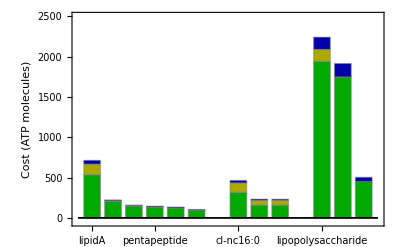

```mathematica
Show[bConstit1,bConstit2,bConstit3]/.Line[{a_,Offset[b_,c_]}]:>Sequence[]
```

### Partitioning of costs across cell wall components

```mathematica
(*atpPoolTotalPositive=totalEnergyFunc[1.41,0.5]*)
```

```mathematica
atpPoolTotalPositive=1.41*totATP
```

5.076×10^10

```mathematica
percentPositiveMemPrec=100*membraneCostPrec/atpPoolTotalPositive;
percentPositiveMemSyn=100*membraneCostSyn/atpPoolTotalPositive;
percentPositiveMemDir=100*membraneCostDir/atpPoolTotalPositive;
```

```mathematica
percentPositivePgnPrec=100*pgnTotalCostPrec/atpPoolTotalPositive;
percentPositivePgnSyn=100*pgnTotalCostSyn/atpPoolTotalPositive;
percentPositivePgnDir=100*pgnTotalCostDir/atpPoolTotalPositive;
```

```mathematica
percentPositiveWtaPrec=100*wtaTotalCostPrec/atpPoolTotalPositive;
percentPositiveWtaSyn=100*wtaTotalCostSyn/atpPoolTotalPositive;
percentPositiveWtaDir=100*wtaTotalCostDir/atpPoolTotalPositive;
```

```mathematica
percentPositiveLtaPrec=100*lipoTeichCostPrec/atpPoolTotalPositive;
percentPositiveLtaSyn=100*lipoTeichCostSyn/atpPoolTotalPositive;
percentPositiveLtaDir=100*lipoTeichCostDir/atpPoolTotalPositive;
```

```mathematica
percentOtherPositive=100-((percentPositiveMemPrec+percentPositiveMemSyn+percentPositiveMemDir)+
(percentPositivePgnPrec+percentPositivePgnSyn+percentPositivePgnDir)+
(percentPositiveWtaPrec+percentPositiveWtaSyn+percentPositiveWtaDir)+
(percentPositiveLtaPrec+percentPositiveLtaSyn+percentPositiveLtaDir));
```

```mathematica
totalCostPieChartPositive=PieChart[{
percentPositiveMemPrec+percentPositiveMemSyn+percentPositiveMemDir,
percentPositivePgnPrec+percentPositivePgnSyn+percentPositivePgnDir,
percentPositiveWtaPrec+percentPositiveWtaSyn+percentPositiveWtaDir,
percentPositiveLtaPrec+percentPositiveLtaSyn+percentPositiveLtaDir,
percentOtherPositive
},SectorOrigin->{Automatic,1},PlotTheme->"Scientific",ChartLegends->{"Membrane","Murein","Wall teichoic acid","Lipoteichoic acid","Cell budget remainder"},ImageSize->Large,ChartStyle->{ColorData["Pastel"],Directive[EdgeForm[{Thick}]]}];
```

```mathematica
directCostPieChartPositive=PieChart[{
percentPositiveMemPrec+percentPositiveMemSyn,percentPositiveMemDir,
percentPositivePgnPrec+percentPositivePgnSyn,percentPositivePgnDir,
percentPositiveWtaPrec+percentPositiveWtaSyn,percentPositiveWtaDir,
percentPositiveLtaPrec+percentPositiveLtaSyn,percentPositiveLtaDir,
percentOtherPositive
},SectorOrigin->{Automatic,1},ImageSize->Large,ChartStyle->{Directive[Opacity[0],EdgeForm[{Gray}]],Directive[EdgeForm[{Dashed,Thick,Dashed}],Opacity[0.45], White]}];
```

```mathematica
bacEnv=Show[totalCostPieChartPositive,directCostPieChartPositive]
```

-Graphics-

```mathematica
100*(wtaTotalCostPrec+wtaTotalCostSyn+wtaTotalCostDir)/atpPoolTotalPositive
100*(membraneCostPrec+membraneCostSyn+membraneCostDir)/atpPoolTotalPositive
100*(pgnTotalCostPrec+pgnTotalCostSyn+pgnTotalCostDir)/atpPoolTotalPositive
100*(lipoTeichCostPrec+lipoTeichCostSyn+lipoTeichCostDir)/atpPoolTotalPositive
```

5.74905

12.317

6.69122

0.911489

```mathematica
(* the total cost of the bacterial envelope *)
cellEnvCostTotal=(wtaTotalCostPrec+wtaTotalCostSyn+wtaTotalCostDir)+
(membraneCostPrec+membraneCostSyn+membraneCostDir)+
(pgnTotalCostPrec+pgnTotalCostSyn+pgnTotalCostDir)+
(lipoTeichCostPrec+lipoTeichCostSyn+lipoTeichCostDir)
```

1.30295×10^10

```mathematica
cellEnvCostTotal/atpPoolTotalPositive (* the fraction of metabolism devoted to production of the envelope *)
```

0.256688

```mathematica
((wtaTotalCostPrec+wtaTotalCostSyn+wtaTotalCostDir)+(pgnTotalCostPrec+pgnTotalCostSyn+pgnTotalCostDir))/atpPoolTotalPositive(* fraction of metabolism devoted to the cell wall *)
```

0.124403